```mathematica
Reduce[Abs[Abs[x-1]-1]==1,x]
```

(-1≤Re[x]<1&&(Im[x]==-√(3+2 Re[x]-Re[x]^2)||Im[x]==√(3+2 Re[x]-Re[x]^2)))||x==1-2 ⅈ||x==1||x==1+2 ⅈ||(1<Re[x]≤3&&(Im[x]==-√(3+2 Re[x]-Re[x]^2)||Im[x]==√(3+2 Re[x]-Re[x]^2)))

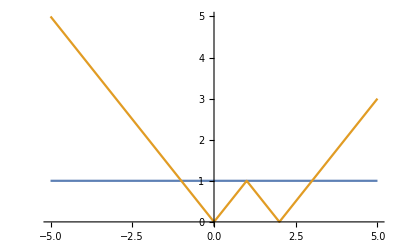

```mathematica
Plot[{1,Abs[Abs[x-1]-1]},{x,-5,5}]
```

# Práctica 2 (27 - 9 - 14) Números reales

```mathematica
Problemas con desigualdades, valor absoluto, acotación, etc.
```

Ejercicio 1. Calcular los valores de x que cumplen 6 - 5 X + X^3 < 2 + x. Acotado? Supremo? Ínfimo? Máximo?

```mathematica
6-5x+x^3<2+x
```

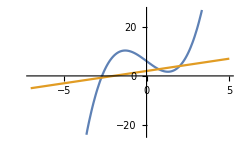

```mathematica
Plot[{6-5x+x^3,2+x},{x,-7,5}]
```

```mathematica
Reduce[6-5x+x^3<2+x,x]
```

x<-1-√3||-1+√3<x<2

La solución (-∞,-1-√3)∪(-1+√3,2). Es un conjunto superiormente (2,3,7,24 son cotas superiores) No es acotado inferiormente. La cota superior más pequela es 2 ( es el supremo). Como no pertenece al conjunto no tiene máximo. Tampoco tiene mínimo ni cotas inferiores.
Menor cota superior posible 2
No tiene cota inferior

```mathematica
Ejercicio 2. Resolver la ecuación |1+|2-x||=3
```

```mathematica
Reduce[Abs[1+Abs[2-x]]==3,x, Reals]
```

x==0||x==4

Las soluciones de la ecuación son el 0 y el 4

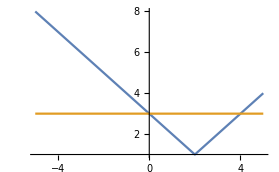

```mathematica
Plot[{Abs[1+Abs[2-x]],3},{x,5,-5}]
```

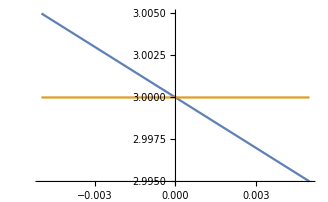

```mathematica
Plot[{Abs[1+Abs[2-x]],3},{x,0.005,-.005}]
```